```mathematica
Clear["Global`*"];
detectCloud[] := StringContainsQ[NotebookDirectory[], "wolframcloud"];
SetDirectory@NotebookDirectory[];
```

# What’s the Best Way to Allocate Members of Congress?

### Every ten years, after the decennial Census, the U.S. reallocates the 435 members of Congress based on updated state populations. This has major implications for both legislation and presidential elections, since a state’s electoral votes are determined the size of its delegation. Is there a better way?

## Loading the Data

While Mathematica has population conveniently built in to state entities through the Wolfram Data Repository, let’s be extra careful and use the same decennial Census figures the government has used for apportionment, as well as the official number of representatives per state allotted every tens years to compare to alternate methods. This data is conveniently organized on Census.gov and gathered in `getPopulationApportionment.nb`

```mathematica
statesByAbbreviation = If[detectCloud[],
	CloudGet["https://www.wolframcloud.com/objects/1a4bfb31-d5d4-49e3-9e04-4cf80e1fae1b"],
	Import["./data/state_population_reps_evs.wl"]
];
```

Let’s check that this loaded correctly with all the data we need

```mathematica
statesByAbbreviation["CA"]
```

<|name→California,abbr→CA,entity→California, United States,population_decennial→<|1910→2377549,1920→3426861,1930→5677251,1940→6907387,1950→10586223,1960→15717204,1970→19953134,1980→23667902,1990→29760021,2000→33871648,2010→37253956|>,representatives→<|1910→11,1920→11,1930→20,1940→23,1950→30,1960→38,1970→43,1980→45,1990→52,2000→53,2010→53|>,evs→<|1910→13,1920→13,1930→22,1940→25,1950→32,1960→40,1970→45,1980→47,1990→54,2000→55,2010→55|>|>

```mathematica
stateAbbrs = Keys@statesByAbbreviation;
```

## How it works now: The Huntington-Hill method

Since the 1940 Census, the United States has used the Huntington-Hill algorithm, known as the “method of equal proportions,” to divvy up the 435 House seats. This begins by allotting one electoral vote to each state, leaving 385 left. The 50 states are then allotted these remaining seats one-by-one according to which one has the highest priority as determined by a simple equation: its population divided by the square root of its current seats times one extra seat (the Geometric Mean):

P/(√(n (1+n)))

["https://en.wikipedia.org/wiki/United_States_congressional_apportionment#The_method_of_equal_proportions"](https://en.wikipedia.org/wiki/United_States_congressional_apportionment#The_method_of_equal_proportions)

Let’s make this equation a function for a given state, getting the 2010 decennial Census data from the data we loaded and feeding it the current number of allocated seats

```mathematica
priorityHuntingtonHill[stateAbbr_, stateEVs_] := 1.0 * statesByAbbreviation[stateAbbr]["population_decennial"]["2010"] / Sqrt[stateEVs * (stateEVs + 1)]
```

The allocation function will assign electoral votes according to the above formula one at a time. We’re also going to explicitly pass the priority function in case we want to try a different one later, which we definitely will, and parameterize all aspects of the allocation algorithm:

To save time, we' re also going to store the priorities until we update the number of seats in a state rather than run 50 square roots 385 times.

total_ is the total number of seats to allocate, defaulting to 435

min_ is the default number of seats that every state begins with, defaulting to 1

priorityFunc_ is the means of determining a state’s priority, defaulting to the Huntington-Hill function defined above

```mathematica
(* We need a list of state abbreviations without DC since it is not factored into allocation -- "Taxation Without Representation!" *)
stateAbbrs50 = Select[stateAbbrs, # ≠ "DC"&];

AllocateOne[evs_, priorities_, priorityFunc_:priorityHuntingtonHill] := (
	topPriority = First[Keys[Reverse[Sort[priorities]]]];
	updatedPriorities = priorities;
	updatedEVs = evs;	
	updatedEVs[topPriority] += 1;
	updatedPriorities[topPriority] = priorityFunc[topPriority, updatedEVs[topPriority]];
	{ updatedEVs, updatedPriorities }
)

calculateAllocations[total_:435, min_:1, priorityFunc_:priorityHuntingtonHill]:= (
	stateEVs = AssociationThread[stateAbbrs50, ConstantArray[1, 50]];
	statePriorities = AssociationThread[stateAbbrs50, priorityFunc[#, 1]& /@ stateAbbrs50];
	While[Total@stateEVs < total, { stateEVs, statePriorities } = AllocateOne[stateEVs, statePriorities, priorityFunc]];
	KeySort@stateEVs
)
```

Here goes nothing:

```mathematica
results = calculateAllocations[];
{ results["AL"], results["KY"], results["CA"] }
Total@results
```

{7,6,53}

435

And let’s see how it performs with a huge House of Representations

```mathematica
bigHouse = calculateAllocations[2000];
```

## Visualizing the outputs

Let’s write a function to compare our calculated allocations to the official ones

```mathematica
houseOfRepresentatives = AssociationThread[stateAbbrs50, statesByAbbreviation[#]["representatives"]["2010"]& /@ stateAbbrs50];
Length@houseOfRepresentatives
```

50

```mathematica
compareAllocations[calculatedEVs_] := (
	diffs = calculatedEVs - houseOfRepresentatives;
	
	(* colors *)
	maxEV = Max[{Max[calculatedEVs], Max[houseOfRepresentatives]}];
	{ minDiff, maxDiff } = MinMax[diffs];
	colorScaleEV = ColorData[{"SiennaTones", "Reverse"}, Rescale[#1, {0, maxEV * 1.25}]]&;
	colorScaleDiff = ColorData["GreenPinkTones", Rescale[#1, {-maxDiff * 1.25, maxDiff * 1.25}]]&;

	(* cells as items *)
	header = Item[#, Alignment -> Right, ItemSize->{9, 1.5}]& /@ { "state", "actual reps", "calculated reps", "difference" };
	houseOfRepresentativesItems = Item[#, Background->colorScaleEV[#]]& /@ houseOfRepresentatives;
	calculatedEVItems = Item[#, Background->colorScaleEV[#]]& /@ calculatedEVs;
	diffItems = Item[#, Background->If[# == 0, White, colorScaleDiff[#]], ItemSize->{2,1.5}]& /@ diffs;
	totals = Item[Style[#, Bold], ItemSize->{4.8, 1.5}]& /@ { "Total", Total@houseOfRepresentatives, Total@calculatedEVs, Total@diffs };

	(* build rows of grids *)
	columns = { Keys@houseOfRepresentatives, Values@houseOfRepresentativesItems, Values@calculatedEVItems, Values@diffItems };	
	parts = First@Partition[Map[Append[columns[[#]], totals[[#]]]&, Range[4]], { 4, UpTo@13 }];
	rows = Map[Flatten, Transpose[{ header, # }]& /@ parts, {2}];
	Column[Grid[#, Frame -> All, ItemSize->All]& /@ rows, Spacings->0.25]
)
compareAllocations[results]
```

state | AK | AL | AR | AZ | CA | CO | CT | DE | FL | GA | HI | IA | ID
actual reps | 1 | 7 | 4 | 9 | 53 | 7 | 5 | 1 | 27 | 14 | 2 | 4 | 2
calculated reps | 1 | 7 | 4 | 9 | 53 | 7 | 5 | 1 | 27 | 14 | 2 | 4 | 2
difference | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
state | IL | IN | KS | KY | LA | MA | MD | ME | MI | MN | MO | MS | MT
actual reps | 18 | 9 | 4 | 6 | 6 | 9 | 8 | 2 | 14 | 8 | 8 | 4 | 1
calculated reps | 18 | 9 | 4 | 6 | 6 | 9 | 8 | 2 | 14 | 8 | 8 | 4 | 1
difference | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
state | NC | ND | NE | NH | NJ | NM | NV | NY | OH | OK | OR | PA | RI
actual reps | 13 | 1 | 3 | 2 | 12 | 3 | 4 | 27 | 16 | 5 | 5 | 18 | 2
calculated reps | 13 | 1 | 3 | 2 | 12 | 3 | 4 | 27 | 16 | 5 | 5 | 18 | 2
difference | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
state | SC | SD | TN | TX | UT | VA | VT | WA | WI | WV | WY | Total
actual reps | 7 | 1 | 9 | 36 | 4 | 11 | 1 | 10 | 8 | 3 | 1 | 435
calculated reps | 7 | 1 | 9 | 36 | 4 | 11 | 1 | 10 | 8 | 3 | 1 | 435
difference | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

Our function worked perfectly. Let’s compare reality to our “Big House”

```mathematica
compareAllocations[bigHouse]
```

ColorData::notent: {SiennaTones,Reverse} is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

General::stop: Further output of ColorData::notent will be suppressed during this calculation.

Total::normal: Nonatomic expression expected at position 1 in Total[bigHouse].

Values::invrl: The argument bigHouse is not a valid Association or a list of rules.

Values::argx: Values called with 2 arguments; 1 argument is expected.

Partition::pdep: Depth 2 requested in object with dimensions {4}.

Transpose::nmtx: The first two levels of {{state,actual reps,calculated reps,difference},{AK,AL,AR,AZ,CA,CO,CT,DE,FL,GA,HI,IA,ID,IL,IN,KS,KY,LA,MA,MD,ME,MI,MN,MO,MS,MT,NC,ND,NE,NH,NJ,NM,NV,NY,OH,OK,OR,PA,RI,SC,SD,TN,TX,UT,VA,VT,WA,WI,WV,WY,«1»}} cannot be transposed.

Transpose::nmtx: The first two levels of … cannot be transposed.

Transpose::nmtx: The first two levels of {{state,actual reps,calculated reps,difference},Values[bigHouse,Total[bigHouse]]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Grid[Transpose[{state,actual reps,calculated reps,difference,AK,AL,AR,AZ,CA,CO,CT,DE,FL,GA,HI,IA,ID,IL,IN,KS,KY,LA,MA,MD,ME,MI,MN,MO,MS,MT,NC,ND,NE,NH,NJ,NM,NV,NY,OH,OK,OR,PA,RI,SC,SD,TN,TX,UT,VA,VT,WA,WI,WV,WY,Total}],Frame→All,ItemSize→All]
Grid[Transpose[{state,actual reps,calculated reps,difference,1,7,4,9,53,7,5,1,27,14,2,4,2,18,9,4,6,6,9,8,2,14,8,8,4,1,13,1,3,2,12,3,4,27,16,5,5,18,2,7,1,9,36,4,11,1,10,8,3,1,435}],Frame→All,ItemSize→All]
Grid[Transpose[{state,actual reps,calculated reps,difference,Values[bigHouse,Total[bigHouse]]}],Frame→All,ItemSize→All]
Grid[Transpose[{state,actual reps,calculated reps,difference,-1+bigHouse,-7+bigHouse,-4+bigHouse,-9+bigHouse,-53+bigHouse,-7+bigHouse,-5+bigHouse,-1+bigHouse,-27+bigHouse,-14+bigHouse,-2+bigHouse,-4+bigHouse,-2+bigHouse,-18+bigHouse,-9+bigHouse,-4+bigHouse,-6+bigHouse,-6+bigHouse,-9+bigHouse,-8+bigHouse,-2+bigHouse,-14+bigHouse,-8+bigHouse,-8+bigHouse,-4+bigHouse,-1+bigHouse,-13+bigHouse,-1+bigHouse,-3+bigHouse,-2+bigHouse,-12+bigHouse,-3+bigHouse,-4+bigHouse,-27+bigHouse,-16+bigHouse,-5+bigHouse,-5+bigHouse,-18+bigHouse,-2+bigHouse,-7+bigHouse,-1+bigHouse,-9+bigHouse,-36+bigHouse,-4+bigHouse,-11+bigHouse,-1+bigHouse,-10+bigHouse,-8+bigHouse,-3+bigHouse,-1+bigHouse,-435+50 bigHouse}],Frame→All,ItemSize→All]

## Analyzing the results

One way to measure the effectiveness of allocation is by measuring the ratio of the population to its number of representatives. We have the population conveniently baked in to the state data

```mathematica
statePopulations = AssociationThread[stateAbbrs50, statesByAbbreviation[#]["population_decennial"]["2010"]& /@ stateAbbrs50];
totalUSPopulation = 308745538; (* https://www.census.gov/data/tables/2010/dec/popchange-data-text.html *)
```

```mathematica
peoplePerRepresentative[allocation_] := (
	perRep = AssociationThread[stateAbbrs50, Round[statePopulations[#] / allocation[#] * 1.0]& /@ stateAbbrs50]
)
houseRatio = peoplePerRepresentative[houseOfRepresentatives];
bigHouseRatio = peoplePerRepresentative[bigHouse];
```

Let’s visualize the distribution of these ratios and use the standard deviation as a barometer

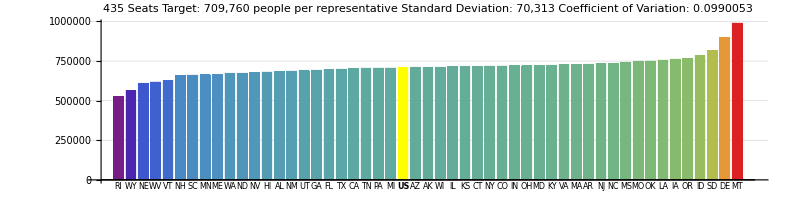

```mathematica
visualizeRatio[allocation_, ratio_] := (
	total = Total@allocation;
	ideal = Round[totalUSPopulation / total];
	ratioWithUS = Append[ratio, "US" -> ideal];
	sd = StandardDeviation[ratio] * 1.0;
	cov = sd / Mean@ratio;
	sdPrint = NumberForm[Round[sd], DigitBlock->3];
	
	colorScale = ColorData["Rainbow", Rescale[#1, MinMax@ratio]]&;
	colorFunction = Function[v, If[v == ideal, Yellow, colorScale[v]]];

	sorted = Sort@ratioWithUS;
	labels = Style[#, If[# == "US", Bold, Plain], FontSize->8]& /@ Keys@sorted;
	
	BarChart[sorted,
		ChartLabels->labels, GridLines->Automatic, ImageSize->{800, Automatic}, AspectRatio->1/4,
		PlotRangePadding -> { -1, 0 }, PlotRange->{ Automatic, Max[sorted] * 1.1 }, ChartStyle->Purple,
		ColorFunctionScaling -> False,
		ColorFunction->colorFunction,
		PlotLabel-> Column[{
			Style[ToString@total <> " Seats", FontSize->20],
			Style["Target: " <> ToString@NumberForm[ideal, DigitBlock -> 3] <> " people per representative", FontSize->14],
			Style["Standard Deviation: " <> ToString[sdPrint], FontSize->14],
			Style["Coefficient of Variation: " <> ToString@cov, FontSize->14]
		}, Alignment->Center]
	]
)
visualizeRatio[houseOfRepresentatives, houseRatio]
```

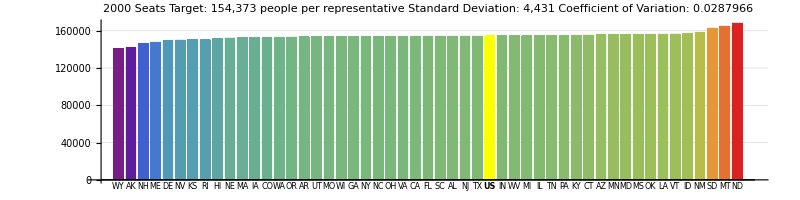

```mathematica
visualizeRatio[bigHouse, bigHouseRatio]
```

## Wrapping up

We now have all the tools we need to play with different ways to configure the House. We’ll import this Notebook into a playpen and get started.